```mathematica
ClearAll[files,importfile,raw]
```

```mathematica
files=FileNames["*.xlsx",NotebookDirectory[]]
```

{/Users/leonidbarinov/Desktop/latexlabs/4 семестр (Оптика)/4.3.1/431.xlsx,/Users/leonidbarinov/Desktop/latexlabs/4 семестр (Оптика)/4.3.1/~$431.xlsx}

```mathematica
importfile=files⟦1⟧
```

/Users/leonidbarinov/Desktop/latexlabs/4 семестр (Оптика)/4.3.1/431.xlsx

```mathematica
raw = Import[importfile];
```

```mathematica
makeAssoc[header_][row_]:=<|header->row//Thread|>;
makeDataset@raw_:=With[{header=raw⟦1⟧,data=raw⟦2;;⟧},
makeAssoc@header/@data
]//Dataset;
```

```mathematica
ClearAll[dataset1,dataset2,dataset1WithErrs,dataset2WithErrs]
```

## Dataset1

```mathematica
dataset1=makeDataset[raw⟦2⟧]
```

Dataset[<>]

```mathematica
dataset1WithErrs=dataset1[All,<|"m"->(#m &),"2zm"-> (Around[#zm, #dzm] &)|>]
```

Dataset[<>]

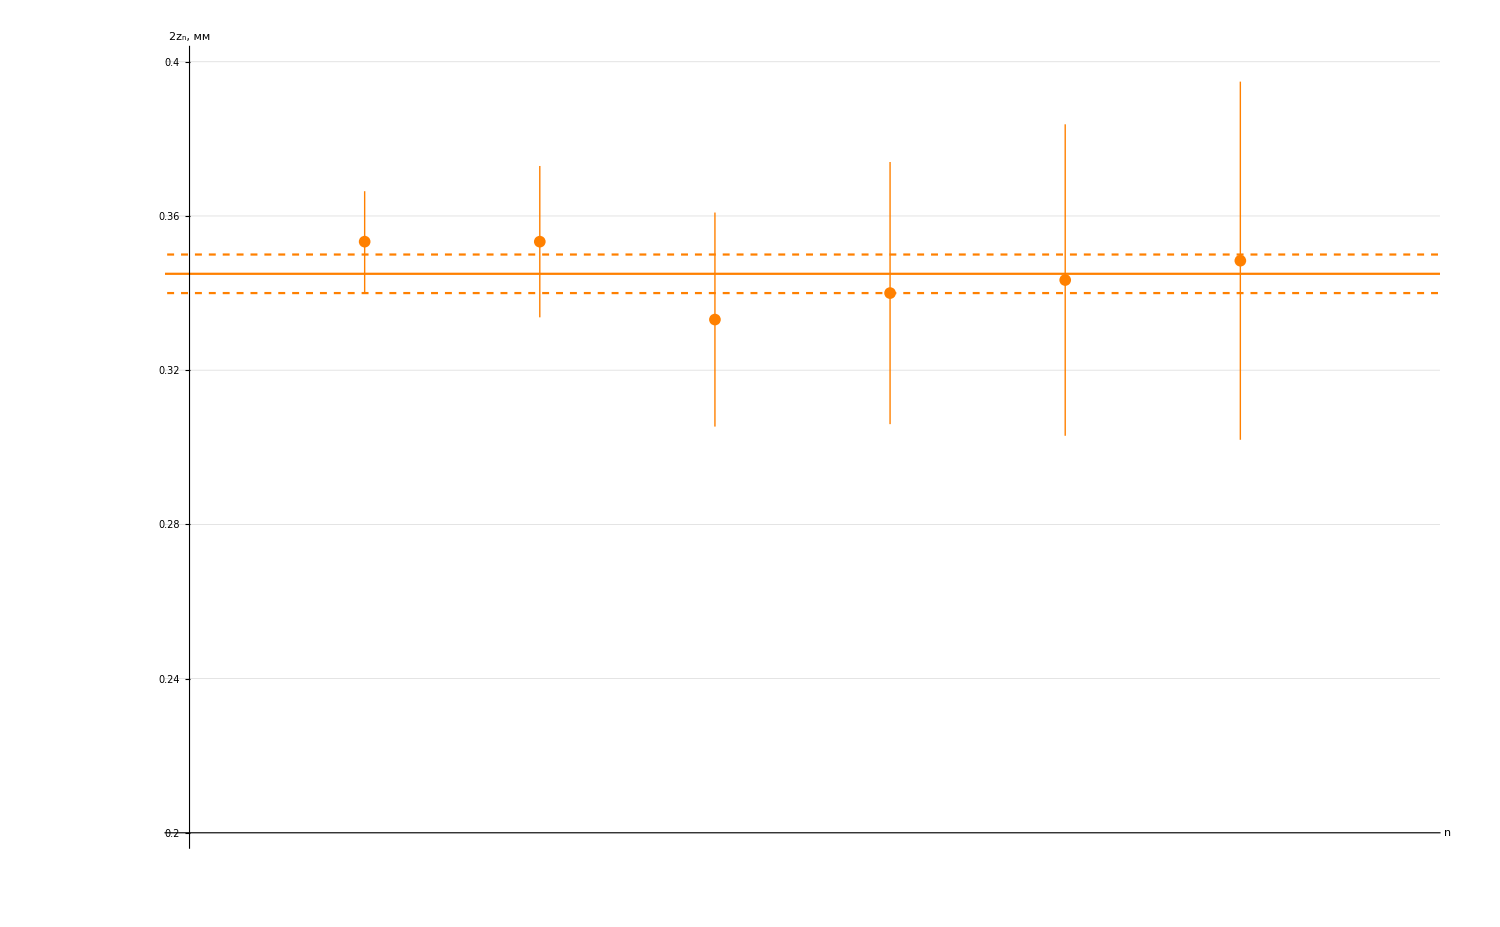

```mathematica
Show[
ListPlot[
{dataset1WithErrs},

PlotRange->{{1,8},{0.2,0.4}},

Ticks-> {Range[-700,700,1],Range[-0.2,0.5,0.02]},

GridLines->{Range[-1000,1000,0.5], Range[-1000,1000,0.005]},

AxesLabel->{Style["n",Large],Style["2z_n, мм",Large]},

TicksStyle->Directive[Black,14],
PlotMarkers->{Automatic,12},
(*AxesStyle->Directive[Arrowheads[{0.02}],Black], *)
AxesStyle->Directive[Arrowheads[0.02],Black],
ImageSize->1500,
LabelStyle->Black,
PlotStyle->Orange
],
Plot[
{0.345,0.35, 0.34},
{x,0, 9},
PlotStyle->{Orange,{Orange,Dashed},{Orange,Dashed}}
(*Callout[{4,0.345},"0.345",{3.6,0.37},LabelStyle->14,Background->None*)]
]
```

```mathematica
ClearAll[files,importfile,raw]
```

```mathematica
files=FileNames["*.xlsx",NotebookDirectory[]]
```

{/Users/leonidbarinov/Desktop/latexlabs/4 семестр (Оптика)/4.3.1/431.xlsx,/Users/leonidbarinov/Desktop/latexlabs/4 семестр (Оптика)/4.3.1/~$431.xlsx}

```mathematica
importfile=files⟦1⟧
```

/Users/leonidbarinov/Desktop/latexlabs/4 семестр (Оптика)/4.3.1/431.xlsx

```mathematica
raw = Import[importfile];
```

```mathematica
makeAssoc[header_][row_]:=<|header->row//Thread|>;
makeDataset@raw_:=With[{header=raw⟦1⟧,data=raw⟦2;;⟧},
makeAssoc@header/@data
]//Dataset;
```

```mathematica
ClearAll[dataset1,dataset2,dataset1WithErrs,dataset2WithErrs]
```

## Dataset 2

```mathematica
dataset2=makeDataset[raw⟦4⟧]
```

Dataset[<>]

```mathematica
dataset2WithErrs=dataset1[All,<|"m"->(#m &),"2zm"-> (Around[#xm, #dxm] &)|>]
```

Dataset[<>]

```mathematica
line2 =LinearModelFit[(Normal@dataset2[All,{"m","xm"}/*Values])⟦1;;6⟧,{1,x},x]
```

FittedModel[0.006+0.181143 x]

```mathematica
line2["ParameterTable"]
```

| Estimate | Standard Error | t-Statistic | P-Value
1 | 0.006 | 0.00550325 | 1.09027 | 0.336874
x | 0.181143 | 0.00180136 | 100.559 | 5.86384×10^-8

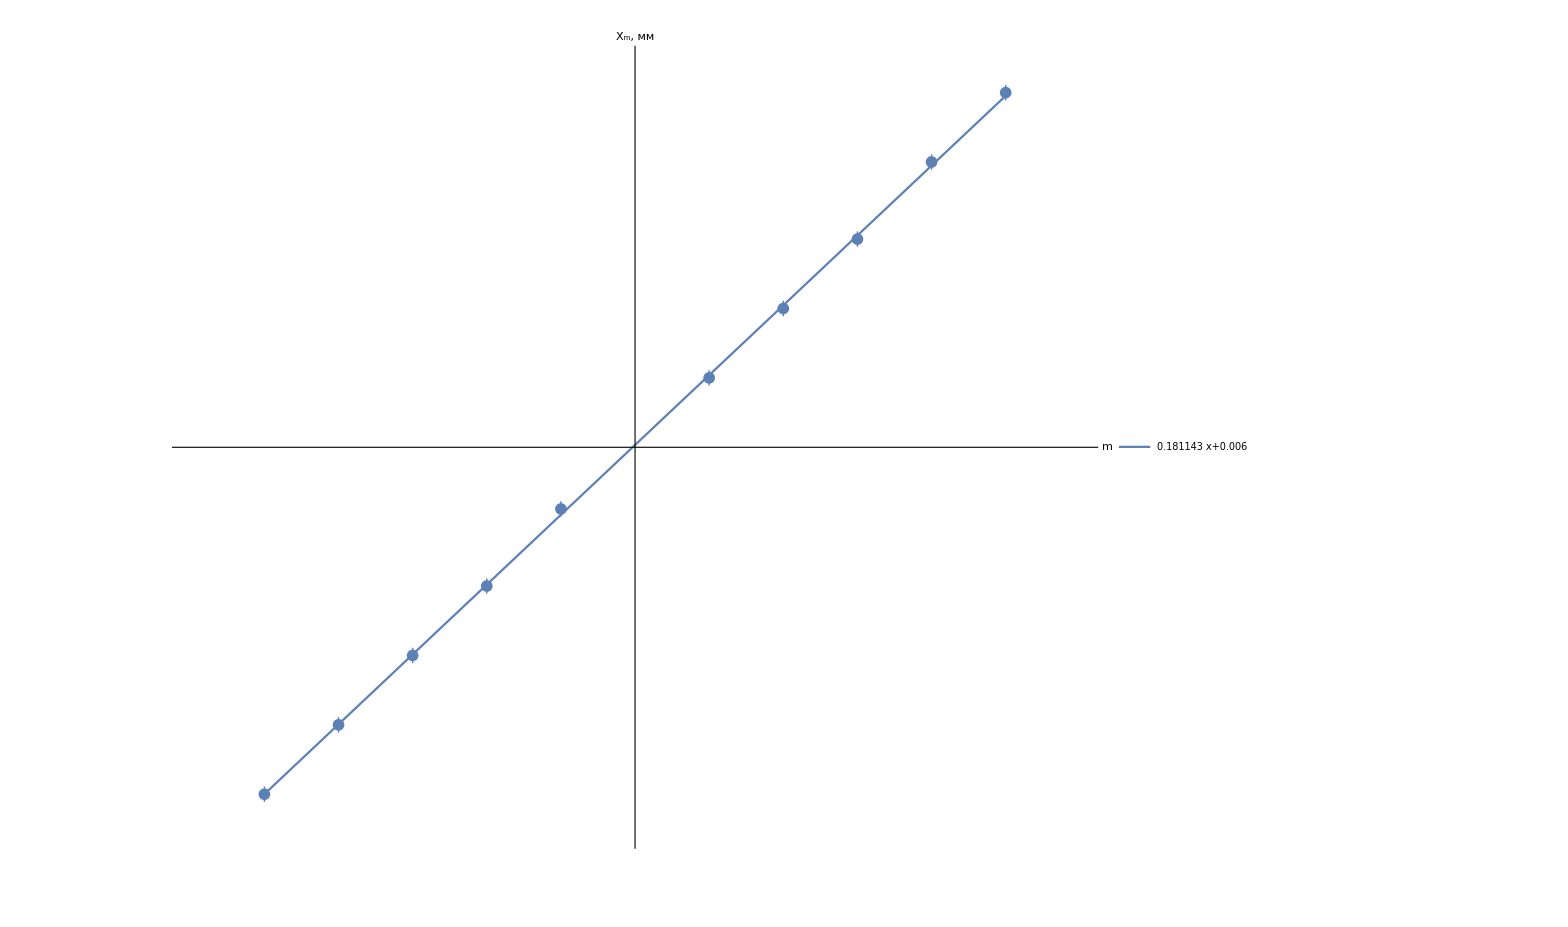

```mathematica
Show[
ListPlot[
{dataset2WithErrs},

PlotRange->{{-6,6},{-1,1}},

Ticks-> {Range[-700,700,1],Range[-10,10,0.1]},

GridLines->{Range[-1000,1000,0.5], Range[-1000,1000,0.05]},

AxesLabel->{Style["m",Large],Style["X_m, мм",Large]},

TicksStyle->Directive[Black,14],
PlotMarkers->{Automatic,12},
(*AxesStyle->Directive[Arrowheads[{0.02}],Black], *)
AxesStyle->Directive[Arrowheads[0.02],Black],
ImageSize->1500,
LabelStyle->Black
(*PlotStyle->Orange*)
],
Plot[
{line2@x},
{x,-5, 5},
PlotLegends->Placed[
LineLegend[
{Normal@line2, line1["ParameterTable"]},
LabelStyle->20
],
{Scaled[0.3],Scaled[0.8]}
]
(*PlotStyle->Darker@Green*)
]
]
```